# Energetski kazalniki, Slovenija, letno

Pridobivanje podatkov

```mathematica
(*pridobil podatke, dodal stolpec z "vrsto" in pa vsemi letnicami ter zamnejal "..." z 0, kjer je bilo to potrebno*)
```

```mathematica
podatki =Import["/Users/spela/Desktop/Matija-Rom/tabela.csv","Table","FieldSeparators"->";",CharacterEncoding->"WindowsEastEurope",HeaderLines->1]//Prepend[#,{"Vrsta",2000,2001,2002,2003,2004,2005,2006,2007, 2008, 2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021}]&//Map[If[#=="...",0,#]&,#,{2}]&//Transpose;
```

```mathematica
tabelaPodatkov=ResourceFunction["DatasetWithHeaders"][podatki]
```

```mathematica
(*
   1: v katerem letu je bila energetska odvisnost maksimalna/minimalna - probu najti vzroke
2:v katerem letu je bila potreba po energiji zagotovljena iz domacih virov min/max - vzroki
*)
```

```mathematica
delezi=tabelaPodatkov//Query[All,{1,16}]//Map[If[#=="-",0,#]&,#,{2}]&
```

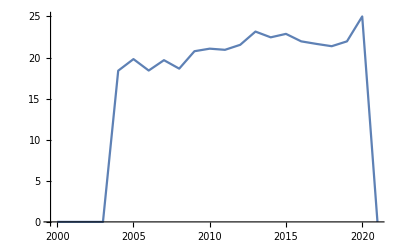

```mathematica
ListLinePlot[delezi]
```